# Диференциално и интегрално смятане със СКА Mathematica

### Граница на редица и граница на функция. Лява и дясна граница.

```mathematica
Limit[(1+1/n)^n,n->Infinity]
```

ⅇ

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
h[x_]:=1/(1+2^(-1/x))
```

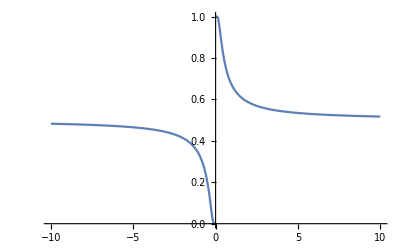

```mathematica
Plot[h[x],{x,-10,10},PlotRange->All]
```

Ако дадена граница не съществува, резултатът от функцията Limit ще бъде Indeterminate. За да пресметнем лява и дясна граница е необходимо да зададем опцията Direction, със съответни стойности “FromBelow” и “FromAbove”.

```mathematica
Limit[h[x],x->0](*По-новите версии на системата, ще върнат като резултат Indeterminate, в случай че границата не съществува*)
```

1

```mathematica
Limit[h[x],x->0 ,Direction->1](*В по-новите версии, опциите на Direction са "FromAbove" и "FromBelow"*)
```

0

```mathematica
Limit[h[x],x->0 ,Direction->-1]
```

1

```mathematica
Sum[n/(n^4+n^2+1),{n,1,Infinity}](*Сума на ред*)
```

1/2

```mathematica
Sum[1/Factorial[n](n/E)^n,{n,1,Infinity}](*Редът не е сходящ*)
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ (ⅇ^-n n^n)/(n!)

```mathematica
Product[i^2,{i,1,n}]
```

(n!)^2

```mathematica
Product[i^2,{i,1,10}]
```

13168189440000

### Производна на функция

```mathematica
f[x_]:=Cos[x] x^6
```

```mathematica
f'[x]
```

6 x^5 Cos[x]-x^6 Sin[x]

```mathematica
f''[x]
```

30 x^4 Cos[x]-x^6 Cos[x]-12 x^5 Sin[x]

```mathematica
D[f[x],{x,4}]
```

360 x^2 Cos[x]-180 x^4 Cos[x]+x^6 Cos[x]-480 x^3 Sin[x]+24 x^5 Sin[x]

```mathematica
D[f[x],{x,4}]/.x->0.5 (*стойност в точка*)
```

40.7174

### Развитие в ред на Тейлър

```mathematica
Series[E^x Cos[2x],{x,0,5}]
```

1+x-(3 x^2)/2-(11 x^3)/6-(7 x^4)/24+(41 x^5)/120+O[x]^6

```mathematica
Series[E^x Cos[2x],{x,0,5}]//Normal  (*Normal извежда полинома до съответната степен без остатъчния член*)
```

1+x-(3 x^2)/2-(11 x^3)/6-(7 x^4)/24+(41 x^5)/120

### Екстремуми на функции

#### Глобални екстремуми

Minimize и Maximize търсят глобален екстремум в инервала (-∞,∞), освен ако допълнителни ограничения за областта на търсене не са зададени. Първият компонент на резултата е екстремалната стойност на фунцкията, а вторият - аргументът, при който се достига тя. Minimize и Maximize могат да работят с функции на произволен брой независими променливи.

```mathematica
Minimize[2 x^2-3x+5,x]
```

{31/8,{x→3/4}}

```mathematica
Minimize[(x y-3)^2+1,{x,y}]
```

{1,{x→-1,y→-3}}

В случай че дадена функция не е ограничена, ще получим предупреждение.

```mathematica
{Minimize[x+2Sin[x],x],Maximize[x+2Sin[x],x]}
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{{-∞,{x→-∞}},{∞,{x→∞}}}

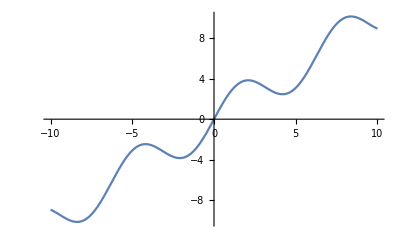

```mathematica
Plot[x+2Sin[x],{x,-10,10}]
```

Можем да зададем допънителни ограничения за областта на търсене във вид на неравенства.

```mathematica
Maximize[x+2Sin[x],-10≤ x≤ 10,x](*Пресмята симоволно*)
```

{√3+(8 π)/3,{x→(8 π)/3}}

NMinimize и NMaximize са съответните функции за числено намиране на глобални екстремуми.

```mathematica
NMaximize[x+2Sin[x],-10≤ x≤ 10,x](*Пресмята числено*)
```

{10.1096,{x→8.37758}}

```mathematica
NMinimize[x+2Sin[x],-10≤ x≤ 10,x]
```

{-10.1096,{x→-8.37758}}

#### Локални екстремуми

FindMaximum/FindMinimum търсят локален екстремум на дадена фунцкия, започвайки от подадена от потребителя стойност, като също могат да приемат ограничения за областта на търсене във вид на неравенства.

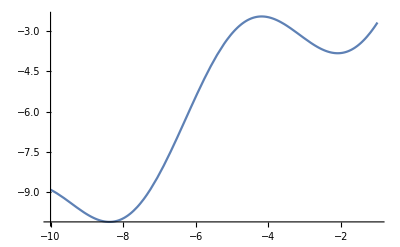

```mathematica
Plot[x+2Sin[x],{x,-10,-1}]
```

```mathematica
FindMaximum[x+2Sin[x],{x,-5}]
```

{-2.45674,{x→-4.18879}}

```mathematica
FindMaximum[x+2Sin[x],{x,-8}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{85.5079,{x→83.7758}}

```mathematica
FindMaximum[{x+2Sin[x],-10≤x≤ -4},{x,-8}]
```

{-2.45674,{x→-4.18879}}

### Интегриране

#### Символно и числено интегриране

Фунцкията Integrate може да се използва за аналитично премсятане на неопределени и определни интеграли. Голяма част от инегралите, които се налага да се решават на практика, обаче, не могат да бъдат решени аналитично. В такъв случай, можем да получим числена апроксимация на стойностие им с помощта на функцията NIntegrate.

```mathematica
Integrate[1/(x^3+1),x] (*Неопределен интеграл*)
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Integrate[1/(x^3+1),{x,0,1}](*Определен инреграл*)
```

1/18 (2 √3 π+Log[64])

```mathematica
NIntegrate[1/(x^3+1),{x,0,1}](*За определени интеграли - дава числена апроксимация*)
```

0.835649

```mathematica
Integrate[Sin[x]/Log[x],{x,2,5}](*Този интеграл, например, не може да бъде решен аналитично*)
```

∫_2^5 Sin[x]/Log[x]ⅆx

```mathematica
NIntegrate[Sin[x]/Log[x],{x,2,5}](*Но може да бъде решен числено*)
```

-0.20523

#### Многократни интеграли

За интегриране върху правоъгълна област, можем просто да изброим границите на интегриране на всяка от променливите:

```mathematica
Integrate[Log[y]/(x y),{x,1,5},{y,1,3}]
```

1/2 Log[3]^2 Log[5]

Можем да интегрираме и върху произволна област. 
Нека да разгледаме задачата за намиране на обема на тялото, образувано от пресичането на равнините z_1=8-3x-2y и z_2=3x+y-4 в първи октант.


-Graphics3D-


Можем да определим границите на интегриране, като използваме факта, че разглеждаме равнините само в първи октант и открием правата, в която те се пресичат:

```mathematica
Reduce[{8-3x-2y== 3x+y-4,x≥0,y≥0},{x,y}]
```

0≤x≤2&&y==4-2 x

```mathematica
Integrate[8-3x-2y-(3x+y-4),{x,0,2},{y,0,4-2x}]
```

16

Друга възможност за пресмятане на интеграла е да дефинираме геометричната област R и да я използваме директно във функцията Integrate.

```mathematica
R=ImplicitRegion[{0≤x≤2,0≤y≤4-2x},{x,y}];
Integrate[8-3x-2y-(3x+y-4),{x,y}∈R] (*Символът "∈", можем да получим като използваме клавишната комбинация Esc + "el" + Esc - това е съкратен запис на командата Element[{x,y},R]*)
```

16

И разбира се, има още една възможност - да използваме троен интеграл:

```mathematica
Integrate[1,{x,0,2},{y,0,4-2x},{z,3x+y-4,8-3x-2y}]//Simplify
R3D=ImplicitRegion[{0≤x≤2,0≤y≤4-2x,3x+y-4 ≤ z≤ 8-3x-2y},{x,y,z}];
Integrate[1,{x,y,z}∈ R3D]//Simplify
```

16

16